### Henderson Hasselbach Model

```mathematica
Clear["`*"]
Reduce[Eliminate[{(H*A/(HA))==Ka,
H*OH==Kw,
CA==HA+A,
H+CB+HA==OH+X,
X==A+HA,
CB==Vb*CBinit/(Va+Vb),
CA==Va*CAinit/(Va+Vb)},{HA,A,OH,CB,CA,X},InverseFunctions->True]]
```

(Kw==0&&H==0&&Ka Va^2+Ka Va Vb≠0)||(H Ka Va≠0&&CAinit==((H+Ka) (H^2 Va-Kw Va+CBinit H Vb+H^2 Vb-Kw Vb))/(H Ka Va)&&Va+Vb≠0)||(Ka==0&&Vb≠0&&H==0&&Kw Va^2+Kw Va Vb≠0)||(Ka==0&&H Vb≠0&&CBinit==-((H^2-Kw) (Va+Vb))/(H Vb)&&Kw Va^2+Kw Va Vb≠0)||(Va==0&&Kw==0&&(H==0||H==-Ka)&&Vb≠0)||(Va==0&&H (H+Ka)≠0&&CBinit==(-H^2+Kw)/H&&Vb≠0)||(Va==0&&Kw≠0&&H==-Ka&&Vb≠0)||(Vb==0&&Ka==0&&(H==0||H==-√Kw||H==√Kw)&&Kw Va≠0)||(Kw==0&&Ka==0&&Vb≠0&&H==0&&Va^2+Va Vb≠0)||(Kw==0&&Ka==0&&H Vb≠0&&CBinit==(-H Va-H Vb)/Vb&&Va^2+Va Vb≠0)||(Vb==0&&Kw==0&&Ka==0&&H==0&&Va≠0)

```mathematica
FullSimplify[Solve[CAinit==((H+Ka) (H^2 Va-Kw Va+CBinit H Vb+H^2 Vb-Kw Vb))/(H Ka Va),Vb]]
```

{{Vb→((H (CAinit Ka-H (H+Ka))+(H+Ka) Kw) Va)/((H+Ka) (H (CBinit+H)-Kw))}}

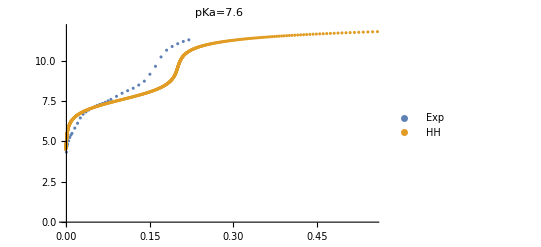

```mathematica
Clear["`*"]
pH=List[4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12];
pH=Table[4.5+0.01*n,{n,1,750}];
Hlist=Table[10^(-pH[[i]]),{i,Length[pH]}];
Va=5;
CAinit=0.004;
CBinit=0.1;
Ka=10^(-7.6);
Kw=10^(-14);
Vb[H_]:=((H (CAinit Ka-H (H+Ka))+(H+Ka) Kw) Va)/((H+Ka) (H (CBinit+H)-Kw));
Vb16={0,1,2,4,6,8,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220};
pH16={4.34,4.7,4.83,5.04,5.25,5.4,5.5,5.83,6.13,6.46,6.69,6.83,6.95,7.05,7.14,7.23,7.3,7.36,7.43,7.52,7.61,7.8,7.99,8.15,8.3,8.5,8.74,9.17,9.66,10.24,10.66,10.89,11.06,11.2,11.3};
ListPlot[{Thread[{Table[Vb16[[i]]/1000,{i,Length[Vb16]}],pH16}],Thread[{Table[Vb[Hlist[[i]]],{i,Length[Hlist]}],pH}]},PlotRange->{Automatic,Automatic},PlotLegends->{"Exp","HH"},PlotLabel->"pKa=7.6"]
```

### Hill Model

```mathematica
Clear["`*"]
Reduce[Eliminate[{(H^n*A/(HA))==Ka^n,
H*OH==Kw,
CA==HA+A,
H+CB+HA==OH+X,
X==A+HA,
CB==Vb*CBinit/(Va+Vb),
CA==Va*CAinit/(Va+Vb)},{HA,A,OH,CB,CA,X},InverseFunctions->True]]
```

(Ka==0&&Re[n]>0&&H==0&&Va+Vb≠0)||(Kw==0&&H==0&&Va+Vb≠0)||(H==0&&Ka==0&&Re[n]>0&&Va+Vb≠0)||(Ka==0&&Re[n]>0&&((H Vb≠0&&CBinit==-((H^2-Kw) (Va+Vb))/(H Vb)&&Va+Vb≠0)||(Vb≠0&&Kw==0&&H==0&&Va+Vb≠0)||(Vb==0&&Va≠0&&(H==-√Kw||H==√Kw))))||(Va==0&&Vb≠0&&((C[1]∈ℤ&&H≠0&&Ka≠0&&Log[H]-Log[Ka]≠0&&n==-(ⅈ π+2 ⅈ π C[1])/(Log[H]-Log[Ka]))||(H==0&&Ka==0&&Re[n]>0)))||(Va==0&&H≠0&&CBinit==(-H^2+Kw)/H&&Vb≠0)||(Va==0&&Kw==0&&H==0&&Vb≠0)||(H Ka^n Va (Va+Vb)≠0&&CAinit==-(Ka^-n (-H^(2+n) Va-H^2 Ka^n Va+H^n Kw Va+Ka^n Kw Va-CBinit H^(1+n) Vb-H^(2+n) Vb-CBinit H Ka^n Vb-H^2 Ka^n Vb+H^n Kw Vb+Ka^n Kw Vb))/(H Va))

```mathematica
Solve[CAinit==-(Ka^-n (-H^(2+n) Va-H^2 Ka^n Va+H^n Kw Va+Ka^n Kw Va-CBinit H^(1+n) Vb-H^(2+n) Vb-CBinit H Ka^n Vb-H^2 Ka^n Vb+H^n Kw Vb+Ka^n Kw Vb))/(H Va),Vb]
```

{{Vb→-((H^(2+n)-CAinit H Ka^n+H^2 Ka^n-H^n Kw-Ka^n Kw) Va)/((H^n+Ka^n) (CBinit H+H^2-Kw))}}

0.63

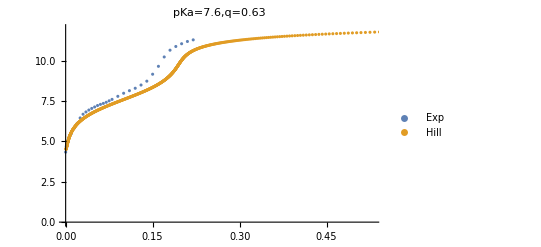

```mathematica
Clear["`*"]
pH=List[4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12];
pH=Table[4.5+0.01*n,{n,1,750}];
Hlist=Table[10^(-pH[[i]]),{i,Length[pH]}];
Va=5;
CAinit=0.004;
CBinit=0.1;
Ka=10^(-7.6);
Kw=10^(-14);
n=0.63
Vb[H_]:=-((H^(2+n)-CAinit H Ka^n+H^2 Ka^n-H^n Kw-Ka^n Kw) Va)/((H^n+Ka^n) (CBinit H+H^2-Kw));
Vb16={0,1,2,4,6,8,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220};
pH16={4.34,4.7,4.83,5.04,5.25,5.4,5.5,5.83,6.13,6.46,6.69,6.83,6.95,7.05,7.14,7.23,7.3,7.36,7.43,7.52,7.61,7.8,7.99,8.15,8.3,8.5,8.74,9.17,9.66,10.24,10.66,10.89,11.06,11.2,11.3};
ListPlot[{Thread[{Table[Vb16[[i]]/1000,{i,Length[Vb16]}],pH16}],Thread[{Table[Vb[Hlist[[i]]],{i,Length[Hlist]}],pH}]},PlotRange->{Automatic,Automatic},PlotLegends->{"Exp","Hill"},PlotLabel->"pKa=7.6,q=0.63"]
```

```mathematica
Clear["`*"]
Reduce[Eliminate[{(H*A/(HA))==Ka*Exp[(1/apl)*(HA/CA)],
H*OH==Kw,
CA==HA+A,
H+B+HA==OH+X,
X==A+HA,
B==Vb*Binit/(Va+Vb),
CA==Va*Ainit/(Va+Vb)},{HA,A,OH,B,CA,X},InverseFunctions->True]]
```

Ainit H Va Log[(H (H^2 Va-Kw Va+Binit H Vb+H^2 Vb-Kw Vb))/(Ka (Ainit H Va-H^2 Va+Kw Va-Binit H Vb-H^2 Vb+Kw Vb))]≠0&&(Va+Vb) (Ainit H Va-H^2 Va+Kw Va-Binit H Vb-H^2 Vb+Kw Vb)≠0&&apl==(Ainit H Va-H^2 Va+Kw Va-Binit H Vb-H^2 Vb+Kw Vb)/(Ainit H Va Log[(H (H^2 Va-Kw Va+Binit H Vb+H^2 Vb-Kw Vb))/(Ka (Ainit H Va-H^2 Va+Kw Va-Binit H Vb-H^2 Vb+Kw Vb))])

#### This equation cannot be solved with current Mathematica method

```mathematica
FullSimplify[Solve[apl==(Ainit H Va-H^2 Va+Kw Va-Binit H Vb-H^2 Vb+Kw Vb)/(Ainit H Va Log[(H (H^2 Va-Kw Va+Binit H Vb+H^2 Vb-Kw Vb))/(Ka (Ainit H Va-H^2 Va+Kw Va-Binit H Vb-H^2 Vb+Kw Vb))]),Vb]]
```

$Aborted

#### Make an approximation, get ride of Vb terms in numerator (Vb<<Va)

```mathematica
Clear["`*"]
FullSimplify[Solve[apl==(Ainit H Va-H^2 Va+Kw Va)/(Ainit H Va Log[(H (H^2 Va-Kw Va+Binit H Vb+H^2 Vb-Kw Vb))/(Ka (Ainit H Va-H^2 Va+Kw Va-Binit H Vb-H^2 Vb+Kw Vb))]),Vb]]
```

{{Vb→ConditionalExpression[((H (Ainit-H-Ainit/(1+(ⅇ^(((Ainit-H) H+Kw)/(Ainit apl H)) Ka)/H))+Kw) Va)/(H (Binit+H)-Kw),-π<Im[((Ainit-H) H+Kw)/(Ainit apl H)]≤π]}}

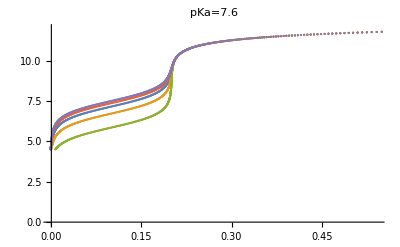

0.3

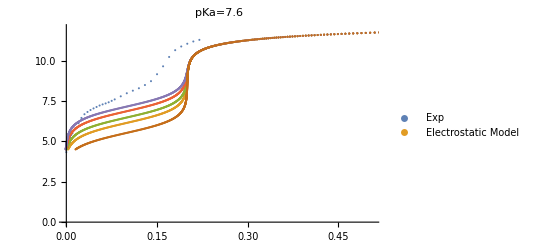

```mathematica
Clear["`*"]
pH=List[4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12];
pH=Table[4.5+0.01*n,{n,1,750}];
Hlist=Table[10^(-pH[[i]]),{i,Length[pH]}];
Va=5;
Ainit=0.004;
Binit=0.1;
Ka=10^(-7.6);
Kw=10^(-14);
Vb[H_,apl_]:=((H (Ainit-H-Ainit/(1+(ⅇ^(((Ainit-H) H+Kw)/(Ainit apl H)) Ka)/H))+Kw) Va)/(H (Binit+H)-Kw)
Vb16={0,1,2,4,6,8,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220};
pH16={4.34,4.7,4.83,5.04,5.25,5.4,5.5,5.83,6.13,6.46,6.69,6.83,6.95,7.05,7.14,7.23,7.3,7.36,7.43,7.52,7.61,7.8,7.99,8.15,8.3,8.5,8.74,9.17,9.66,10.24,10.66,10.89,11.06,11.2,11.3};
ListPlot[{Thread[{Table[Vb[Hlist[[i]],1],{i,Length[Hlist]}],pH}],Thread[{Table[Vb[Hlist[[i]],0.5],{i,Length[Hlist]}],pH}],Thread[{Table[Vb[Hlist[[i]],0.25],{i,Length[Hlist]}],pH}],Thread[{Table[Vb[Hlist[[i]],2],{i,Length[Hlist]}],pH}],Thread[{Table[Vb[Hlist[[i]],5],{i,Length[Hlist]}],pH}]},PlotRange->{Automatic,Automatic},PlotLabel->"pKa=7.6"]
aplinit=0.3
ListPlot[{Thread[{Table[Vb16[[i]]/1000,{i,Length[Vb16]}],pH16}],Thread[{Table[Vb[Hlist[[i]],aplinit],{i,Length[Hlist]}],pH}],Thread[{Table[Vb[Hlist[[i]],1.3*aplinit],{i,Length[Hlist]}],pH}],Thread[{Table[Vb[Hlist[[i]],2*aplinit],{i,Length[Hlist]}],pH}],Thread[{Table[Vb[Hlist[[i]],(1/0.3)*aplinit],{i,Length[Hlist]}],pH}],Thread[{Table[Vb[Hlist[[i]],.7*aplinit],{i,Length[Hlist]}],pH}]},PlotRange->{Automatic,Automatic},PlotLegends->{"Exp","Electrostatic Model"},PlotLabel->"pKa=7.6"]
```